## Elegir datos aleatoriamente a partir de una distribución

```mathematica
RandomReal[]
```

0.0490867

```mathematica
SeedRandom[12]
```

RandomGeneratorState[…]

```mathematica
xx8=AbsoluteTime[]
```

3.906088654780315×10^9

```mathematica
IntegerPart@AbsoluteTime[]
```

3906088673

```mathematica
IntegerPart@xx8
```

3906088654

```mathematica
SeedRandom[IntegerPart@AbsoluteTime[]]
```

RandomGeneratorState[…]

```mathematica
?*Distribution
```

```mathematica
xx9=?*Distribution
```

```mathematica
Dimensions[xx9]
```

{2}

```mathematica
xx9[[1,1,2]]//Length
```

167

```mathematica
𝒟u=UniformDistribution[]
```

UniformDistribution[{0,1}]

```mathematica
AbsoluteTiming[listaDu=RandomVariate[𝒟u,50000000];]
```

{0.433367,Null}

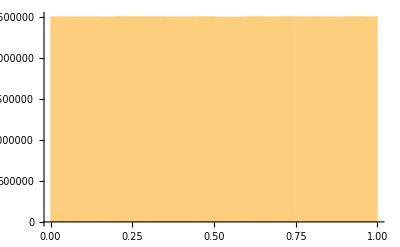

```mathematica
Histogram@listaDu
```

```mathematica
𝒟=NormalDistribution[]
```

NormalDistribution[0,1]

```mathematica
PDF[𝒟,x]
```

(ⅇ^(-x^2/2))/(√(2 π))

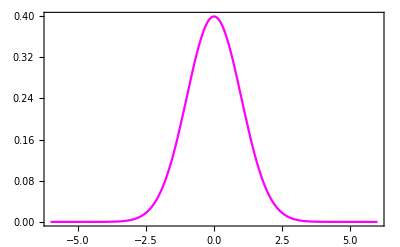

```mathematica
grN=Plot[PDF[𝒟,x],{x,-6,6},Frame->True,Axes->False,PlotStyle->Magenta]
```

```mathematica
x
```

x

```mathematica
x=5
```

5

```mathematica
Clear[x]
```

```mathematica
x=.
```

```mathematica
PDF[𝒟,x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Integrate[PDF[𝒟,x],{x, -∞,X}]
```

1/2 (1+Erf[X/(√2)])

```mathematica
Integrate[PDF[𝒟,x],{x, -∞,∞}]
```

1

```mathematica
CDF[𝒟,x]
```

1/2 Erfc[-x/(√2)]

```mathematica
FullSimplify[%58==%56/.X->x]
```

True

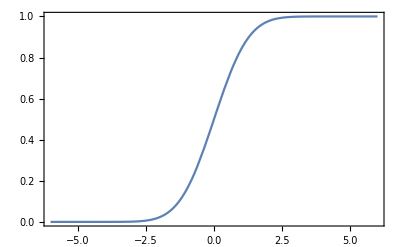

```mathematica
grCN=Plot[CDF[𝒟,x],{x,-6,6},Frame->True,Axes->False]
```

```mathematica
Manipulate[Show[grN,Plot[PDF[𝒟,x],{x,-6,X},Filling->Bottom],FrameLabel->CDF[𝒟,X]],{X,-5.9,6}]
```

```mathematica
Manipulate[Show[grCN,Plot[CDF[𝒟,x],{x,-6,X},Filling->Bottom],FrameLabel->CDF[𝒟,X]],{X,-4,6}]
```

```mathematica
x0=RandomReal[]
```

0.807381

```mathematica
CDF[𝒟,x]
```

1/2 Erfc[-x/(√2)]

```mathematica
Solve[CDF[𝒟,x]==x0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.868284}}

```mathematica
FindRoot[CDF[𝒟,x]==x0,{x,1.1}]
```

{x→0.868284}

```mathematica
AbsoluteTiming[randNormal=ParallelTable[FindRoot[CDF[𝒟,y]==RandomReal[],{y,0.}][[1,2]],{400000}];]
```

{33.9259,Null}

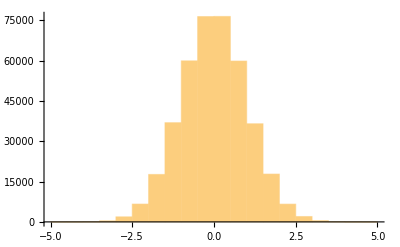

```mathematica
Histogram@randNormal
```

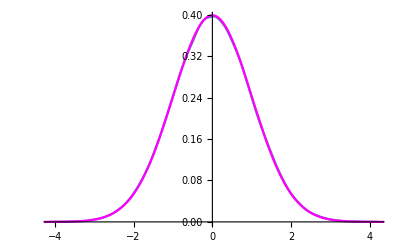

```mathematica
Show[SmoothHistogram@randNormal,grN]
```

```mathematica
𝒟
```

NormalDistribution[0,1]

```mathematica
AbsoluteTiming[dat=RandomVariate[𝒟,10000000];]
```

{0.187391,Null}

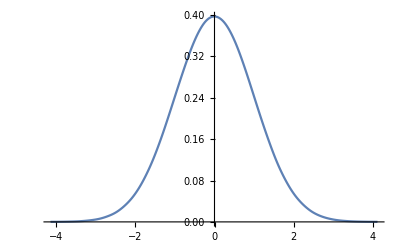

```mathematica
SmoothHistogram@dat
```

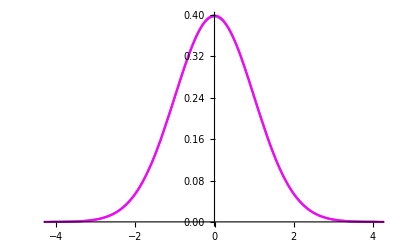

```mathematica
Show[SmoothHistogram@dat,grN]
```

```mathematica
Manipulate[SmoothHistogram[RandomVariate[NormalDistribution[μ,σ],100000]],{{μ,.0},-1.,1.,.05},{{σ,1.},0.05,5,.05}]
```

```mathematica
PDF[MaxwellDistribution[σ],x]
```

Piecewise[{{(ⅇ^(-x^2/(2 σ^2)) √(2/π) x^2)/σ^3, x>0}, {0, True}}]

```mathematica
Manipulate[Plot[PDF[MaxwellDistribution[σ],x],{x,0,100},PlotRange->All],{{σ,1.},.1,50,.1}]
```

```mathematica
Manipulate[Plot[CDF[MaxwellDistribution[σ],x],{x,0,100},PlotRange->All],{{σ,20.},.1,50,.1}]
```

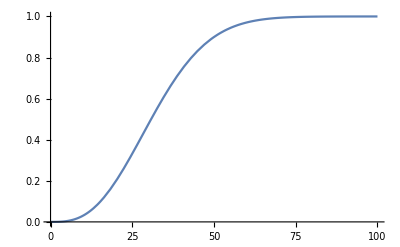

```mathematica
Plot[CDF[MaxwellDistribution[20],x],{x,0,100}]
```

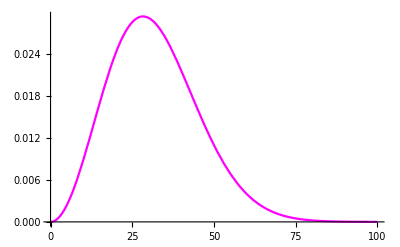

```mathematica
max1=Plot[PDF[MaxwellDistribution[20],x],{x,0,100},PlotStyle->Magenta]
```

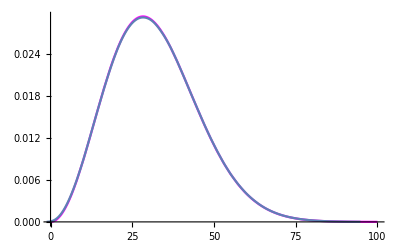

```mathematica
Show[max1,SmoothHistogram@RandomVariate[MaxwellDistribution[20],10000000]]
```

```mathematica
𝒟=VonMisesDistribution[0,1.5];
```

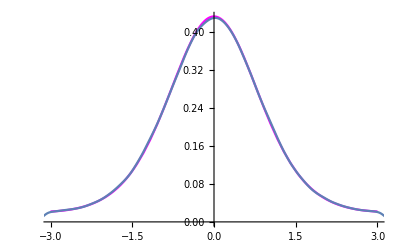

```mathematica
Show[Plot[PDF[𝒟,x],{x,-3,3},PlotStyle->Magenta],SmoothHistogram@RandomVariate[𝒟,1000000]]
```

```mathematica
𝒟=KumaraswamyDistribution[2,3/4];
```

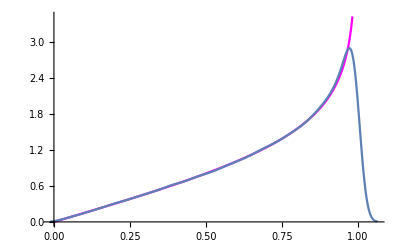

```mathematica
Show[Plot[PDF[𝒟,x],{x,0,1},PlotStyle->Magenta],SmoothHistogram@RandomVariate[𝒟,1000000],PlotRange->All]
```

```mathematica
data=RandomVariate[𝒟,10000000];
```

```mathematica
dist=SmoothKernelDistribution[data,Automatic,{"Bounded",{0,1},"Gaussian"}];
```

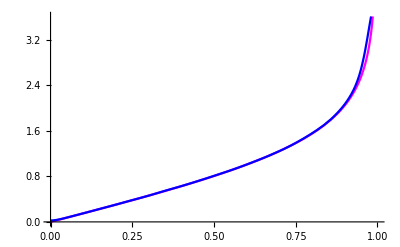

```mathematica
Plot[{PDF[𝒟,x],PDF[dist,x]},{x,0,1},PlotStyle->{Magenta,Blue}]
```